Integrale da valutare

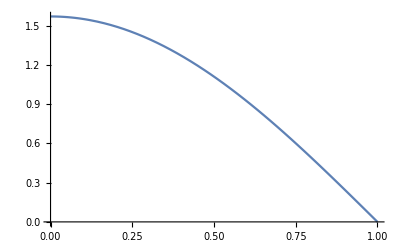

```mathematica
Plot[Pi/2*Cos[Pi*x/2],{x,0,1}]
```

L’idea iniziale è stata quella di scegliere come p(x) non normalizzata l’espansione del coseno al secondo ordine

```mathematica
f[x_]=1-Pi^2/8 x^2
```

1-(π^2 x^2)/8

```mathematica
p[x_]=f[x]/Integrate[f[x],{x,0,1}]
```

(1-(π^2 x^2)/8)/(1-π^2/24)

Tuttavia il calcolo della varianza ha mostrato che con questa scelta di p(x) normalizzata si ha che la varianza della funzione diverge.

```mathematica
Integrate[(Pi/2*Cos[Pi x/2 ]/p[x])^2 p[x],{x,0,1}]-Integrate[Pi/2*Cos[Pi x/2],{x,0,1}]^2
```

Integrate::idiv: Integral of -(2 π^2 Cos[(π x)/2]^2)/(-8+π^2 x^2)+(π^4 Cos[(π x)/2]^2)/(12 (-8+π^2 x^2)) does not converge on {0,1}.

-1+∫_0^1 (π^2 (1-π^2/24) Cos[(π x)/2]^2)/(4 (1-(π^2 x^2)/8))ⅆx

Varianza dell’integrale con p(x)= x^(1/2) -> Varianza molto più alta dell’integrale da calcolare

```mathematica
N[Integrate[(Pi/2*Cos[Pi x/2]/(2/3  x^(1/2)))^2  2/3  x^(1/2),{x,0,1}]-Integrate[Pi/2*Cos[Pi x/2],{x,0,1}]^2]
```

4.08525

Varianza dell’integrale con p(x)= Cx^r

```mathematica
N[Integrate[(Pi/2*Cos[Pi x/2]/(C  x^r))^2  C  x^r,{x,0,1}]-Integrate[Pi/2*Cos[Pi x/2],{x,0,1}]^2]
```

ConditionalExpression[-1.+(24.3523 HypergeometricPFQ[{1.5-0.5 r},{1.5,2.5-0.5 r},-2.4674])/(C (6.-8. r+2. r^2)),Re[r]<1.]

Varianza dell’integrale da calcolare (p(x)=1)

```mathematica
N[Integrate[(Pi/2*Cos[Pi x/2])^2 ,{x,0,1}]-Integrate[Pi/2*Cos[Pi x/2],{x,0,1}]^2]
```

0.233701

Si vede che la scelta di p(x)=x^(-1/4) normalizzata permette di avere una varianza inferiore a quella dell’integrale dato (con p(x)=1).

```mathematica
N[Integrate[(Pi/2*Cos[Pi x/2]/(3/4  x^(-1/4)))^2  (3/4 x^(-1/4)),{x,0,1}]-Integrate[Pi/2*Cos[Pi x/2],{x,0,1}]^2]
```

0.141254+0. ⅈ

Si sceglie p(x)=3/2 1-x^2

```mathematica
N[Integrate[(Pi/2*Cos[Pi x/2]/(3(1-x^2)/2))^2  (3(1-x^2)/2),{x,0,1}]-Integrate[Pi/2*Cos[Pi x/2],{x,0,1}]^2]
```

0.00244478

Si vede che anche con questa scelta di p(x)= Pi/2 Exp(-Pi/2 x)/(1-Exp[-Pi/2]) si riduce la varianza

```mathematica
N[Integrate[(Pi/2*Cos[Pi x/2]/(Pi/2 Exp[-Pi/2 x]/(1-Exp[-Pi/2])))^2  (Pi/2 Exp[-Pi/2 x]/(1-Exp[-Pi/2])),{x,0,1}]-Integrate[Pi/2*Cos[Pi x/2],{x,0,1}]^2]
```

0.0489187

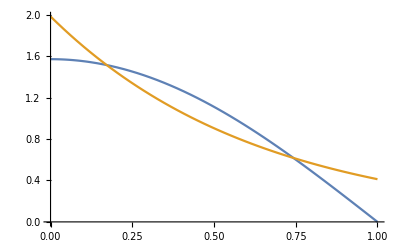

```mathematica
Plot[{Pi/2*Cos[Pi*x/2],Pi/2 Exp[-Pi/2 x]/(1-Exp[-Pi/2])},{x,0,1}]
```